# Large volume scattering diagram for KP2

```mathematica
SetDirectory[NotebookDirectory[]];
<<P2Scattering`
<<CoulombHiggs`
<<MaTeX`
```

P2Scattering 1.3 - A package for evaluating DT invariants on K_{P^2}

CoulombHiggs 6.3 - A package for evaluating quiver invariants

## Geometry of local scattering

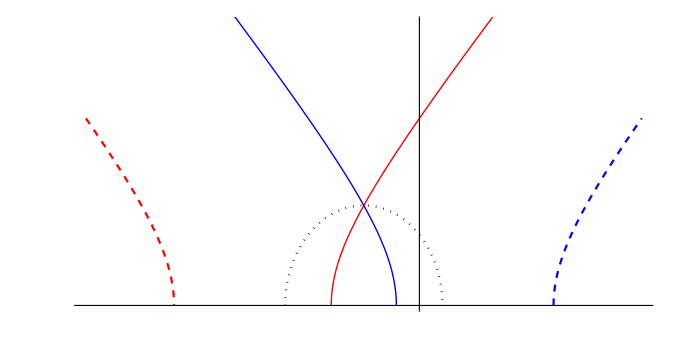

```mathematica
With[{gam1=-2Ch[-2]+Ch[-1]/.repCh,gam2=-Ch[-1]+2Ch[0]/.repCh},
Show[PlotWallRay[gam1,gam2,0,{-6,4,4}],Ticks->{{{-1-√2,MaTeX["s_{\\gamma,\\gamma'}-R"]},{-1+√2,
MaTeX["s_{\\gamma,\\gamma'}+R"]},{GenSlope[gam1]+Sqrt[2Disc[gam1]],MaTeX["\\mu'+\\sqrt{2\\Delta'}"]},
{GenSlope[gam1]-Sqrt[2Disc[gam1]],MaTeX["\\mu'-\\sqrt{2\\Delta'}"]},
{GenSlope[gam2]+Sqrt[2Disc[gam2]],MaTeX["\\mu+\\sqrt{2\\Delta}"]},
{GenSlope[gam2]-Sqrt[2Disc[gam2]],MaTeX["\\mu-\\sqrt{2\\Delta}"]}},None},AspectRatio->1/2]]
```

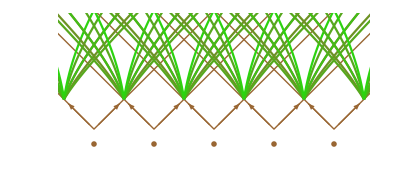

```mathematica
Show[Graphics[Table[{Brown,Arrow[{{m,0},{m+1/2,1/2}},.1],Arrow[{{m,0},{m-1/2,1/2}},.1],Line[{{m-2,2},{m,0},{m+2,2}}],Text[MaTeX["\\pm\\mathcal{O}("<>ToString[m]<>")"] (*"O("<>ToString[m]<>")"*),{m,-.25}]},{m,-2,2}]],Table[Plot[Rayt[p{1,m,1+m(m+3)/2}-q{1,m+1,1+(m+1)(m+4)/2},s,0],{s,m+1/2,m+2},PlotStyle->TreeHue[7,p+q-2]],{p,1,4},{q,1,p-1},{m,-3,2}],Table[Plot[Rayt[p{1,m,1+m(m+3)/2}-q{1,m+1,1+(m+1)(m+4)/2},s,0],{s,m-1,m+1/2},PlotStyle->TreeHue[7,p+q-2]],{q,1,4},{p,1,q-1},{m,-3,2}],PlotRange->{{-2.5,2.5},{-.3,1.9}},Axes->Automatic,AxesLabel->{s,t}]
```

## Rank 1 / Hilbert scheme of n points on P2

```mathematica
(* Prediction from Goettsche's formula *)
NMax=16;
th1[q_,y_]:=-I Sum[(-1)^n q^(1/2(n-1/2)^2) y^(n-1/2),{n,-NMax,NMax}]; 
eta[q_]:=q^(1/24)*(1+Sum[(-1)^n*(q^(n*(3*n-1)/2)+q^(n*(3*n+1)/2)),{n,1,NMax}]);
GenSeries=Series[Simplify[Assuming[{y>1,q<1},Series[I q^((b2+2)/24)(y-1/y)/eta[q]^(b2-1)/th1[q,y^2],{q,0,NMax}]]/.b2->1],{y,Infinity,0}]
```

1+(y^2+1+O[1/y]^1) q+(y^4+2 y^2+3+O[1/y]^1) q^2+(y^6+2 y^4+5 y^2+6+O[1/y]^1) q^3+(y^8+2 y^6+6 y^4+10 y^2+13+O[1/y]^1) q^4+(y^10+2 y^8+6 y^6+12 y^4+21 y^2+24+O[1/y]^1) q^5+(y^12+2 y^10+6 y^8+13 y^6+26 y^4+39 y^2+47+O[1/y]^1) q^6+(y^14+2 y^12+6 y^10+13 y^8+28 y^6+49 y^4+74 y^2+83+O[1/y]^1) q^7+(y^16+2 y^14+6 y^12+13 y^10+29 y^8+54 y^6+94 y^4+131 y^2+150+O[1/y]^1) q^8+(y^18+2 y^16+6 y^14+13 y^12+29 y^10+56 y^8+105 y^6+167 y^4+232 y^2+257+O[1/y]^1) q^9+(y^20+2 y^18+6 y^16+13 y^14+29 y^12+57 y^10+110 y^8+189 y^6+298 y^4+395 y^2+440+O[1/y]^1) q^10+(y^22+2 y^20+6 y^18+13 y^16+29 y^14+57 y^12+112 y^10+200 y^8+339 y^6+508 y^4+668 y^2+729+O[1/y]^1) q^11+(y^24+2 y^22+6 y^20+13 y^18+29 y^16+57 y^14+113 y^12+205 y^10+362 y^8+584 y^6+861 y^4+1099 y^2+1204+O[1/y]^1) q^12+(y^26+2 y^24+6 y^22+13 y^20+29 y^18+57 y^16+113 y^14+207 y^12+373 y^10+627 y^8+994 y^6+1418 y^4+1795 y^2+1939+O[1/y]^1) q^13+(y^28+2 y^26+6 y^24+13 y^22+29 y^20+57 y^18+113 y^16+208 y^14+378 y^12+650 y^10+1075 y^8+1647 y^6+2317 y^4+2873 y^2+3105+O[1/y]^1) q^14+(y^30+2 y^28+6 y^26+13 y^24+29 y^22+57 y^20+113 y^18+208 y^16+380 y^14+661 y^12+1119 y^10+1790 y^8+2701 y^6+3707 y^4+4560 y^2+4887+O[1/y]^1) q^15+(y^32+2 y^30+6 y^28+13 y^26+29 y^24+57 y^22+113 y^20+208 y^18+381 y^16+666 y^14+1142 y^12+1873 y^10+2951 y^8+4339 y^6+5883 y^4+7130 y^2+7634+O[1/y]^1) q^16+O[q]^17

```mathematica
(* number of points on P2 *)
n=7;
```

```mathematica
(* Looking for all possible trees *)
LiTrees=ScanAllTrees[{1,0,1-n},{-n-1/2,n+1/2}]
```

Possible values of {mmin,mmax}:{{-7,-6},{-7,-5},{-7,-4},{-6,-5},{-6,-4},{-6,-3},{-5,-4},{-5,-3},{-5,-2},{-4,-3},{-4,-2},{-4,-1},{-3,-2},{-3,-1},{-3,0},{-2,-1},{-2,0},{-1,0}}

41 possible sets of constituents out of 10065 trials

{{{-Ch[-4],Ch[-3]},Ch[-1]},{-2 Ch[-3],3 Ch[-2]}}

```mathematica
(* alternately, use precomputed list*)
LiTrees=LVTrees[{1,0,1-n}]
```

{{{-Ch[-8],Ch[-7]},Ch[-1]},{{-Ch[-7],Ch[-6]},{-Ch[-3],2 Ch[-2]}},{{-Ch[-6],Ch[-5]},{{-Ch[-4],Ch[-3]},Ch[-2]}},{{-2 Ch[-5],2 Ch[-4]},Ch[-2]},{{-Ch[-5],Ch[-4]},{-2 Ch[-4],3 Ch[-3]}},{{-Ch[-5],Ch[-3]},{-Ch[-4],2 Ch[-3]}},{-Ch[-5],{-Ch[-4],3 Ch[-3]}}}

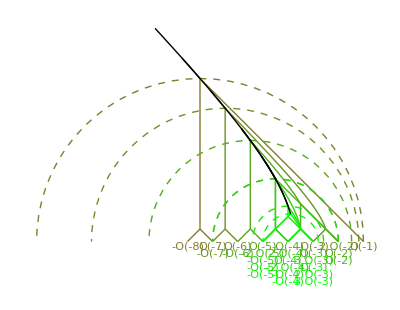

```mathematica
(* Scattering diagram in (s,t) plane, psi=0 *)
ScattDiagLV[LiTrees,0]
```

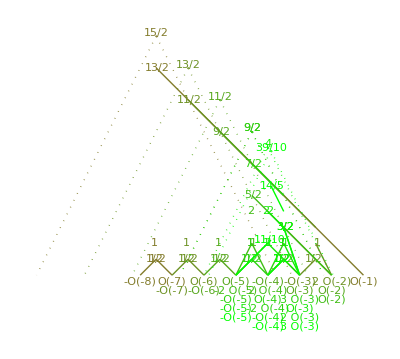

```mathematica
(* Diagram in (s,φ) plane *)
ScattPhi[LiTrees]
```

```mathematica
IndKr=ScattIndex[LiTrees]
```

Beware, non-primitive state

{Kr_3[1,1]^2,Kr_3[1,1]^2 Kr_3[1,2],Kr_3[1,1]^4,Kr_3[1,2] Kr_3[2,2],Kr_3[1,1]^2 Kr_3[2,3],Kr_3[1,2] Kr_6[1,1]^2,Kr_3[1,3] Kr_15[1,1]}

```mathematica
Ind=EvaluateKronecker[IndKr];
Limit[Ind,y->1]
Series[Ind,{y,Infinity,0}]
(* compare to generating series *)
Simplify[SeriesCoefficient[GenSeries,n]-Plus@@Ind]
```

{9,27,81,-18,117,108,15}

{y^4+2 y^2+3+O[1/y]^1,y^6+3 y^4+6 y^2+7+O[1/y]^1,y^8+4 y^6+10 y^4+16 y^2+19+O[1/y]^1,-y^7-2 y^5-3 y^3-3 y+O[1/y]^1,y^10+3 y^8+8 y^6+14 y^4+21 y^2+23+O[1/y]^1,y^12+3 y^10+6 y^8+9 y^6+12 y^4+15 y^2+16+O[1/y]^1,y^14+y^12+y^10+y^8+y^6+y^4+y^2+1+O[1/y]^1}

-69-1/y^14-2/y^12-5/y^10-11/y^8+1/y^7-23/y^6+2/y^5-41/y^4+3/y^3-61/y^2+3/y+3 y-61 y^2+3 y^3-41 y^4+2 y^5-23 y^6+y^7-11 y^8-5 y^10-2 y^12-y^14+SeriesCoefficient[GenSeries,7]

```mathematica
(* When some internal charges are non-primitive, more care is needed to compute the index : *)L21=P2HiggsBranchFormula[{{0,3,0},{-3,0,3},{0,-3,0}},{3,2,1},{2,2,1}];
L31=P2HiggsBranchFormula[{{0,3,0},{-3,0,3},{0,-3,0}},{3,2,1},{3,3,1}];
L22=P2HiggsBranchFormula[{{0,3,0},{-3,0,3},{0,-3,0}},{3,2,-1},{2,2,2}];
Ind=EvaluateKronecker[IndKr/.{Subscript[Kr, 3][2,2]^2->L222,Subscript[Kr, 3][2,2]->L12/Subscript[Kr, 3][1,2] , Subscript[Kr, 3][3,3]->L13/Subscript[Kr, 3][1,3]}]/.{L12->L21,L13->L31,L222->L22};
Limit[Ind,y->1]
Series[Ind,{y,Infinity,0}]
(* compare to generating series *)
Simplify[SeriesCoefficient[GenSeries,n]-Plus@@Ind]
```

{9,27,81,72,117,108,15}

{y^4+2 y^2+3+O[1/y]^1,y^6+3 y^4+6 y^2+7+O[1/y]^1,y^8+4 y^6+10 y^4+16 y^2+19+O[1/y]^1,y^10+2 y^8+5 y^6+8 y^4+13 y^2+14+O[1/y]^1,y^10+3 y^8+8 y^6+14 y^4+21 y^2+23+O[1/y]^1,y^12+3 y^10+6 y^8+9 y^6+12 y^4+15 y^2+16+O[1/y]^1,y^14+y^12+y^10+y^8+y^6+y^4+y^2+1+O[1/y]^1}

O[1/y]^1

## D2-D0 indices - Sheaves supported on degree d curve

```mathematica
d=3; chi=1;
```

```mathematica
(* Gieseker wall, according to Woolf *)
Module[{a,k,eta},
a=chi-3/2d+1/2d^2;
k=Round[a/d];eta=a-d Round[a/d];
s0=k+eta/d-d/2;
t0=d/2-Abs[eta]/d;
{k,eta,{s0,t0}}]
```

{0,1,{-7/6,7/6}}

```mathematica
(* scan for all trees - this may take a long time *)
LiTrees=ScanAllTrees[{0,d,chi},{s0,t0+.1}]
```

Possible values of {mmin,mmax}:{{-3,-2},{-3,-1},{-3,0},{-2,-1},{-2,0},{-2,1},{-1,0},{-1,1},{0,1}}

2 possible sets of constituents out of 1755 trials

{{{-2 Ch[-2],Ch[-1]},Ch[0]}}

```mathematica
(* alternately, use precomputed list*)
LiTrees=LVTrees[{0,d,chi}]
```

{{{-2 Ch[-2],Ch[-1]},Ch[0]}}

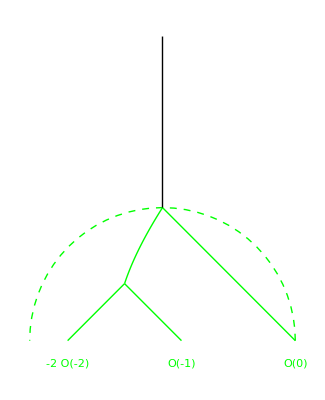

```mathematica
(* Scattering diagram in (s,t) plane, psi=0 *)
ScattDiagLV[LiTrees,0]
```

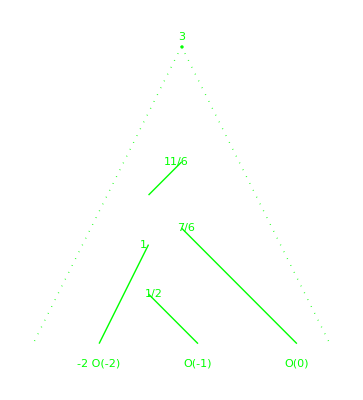

```mathematica
(* Diagram in (s,φ) plane *)
ScattPhi[LiTrees]
```

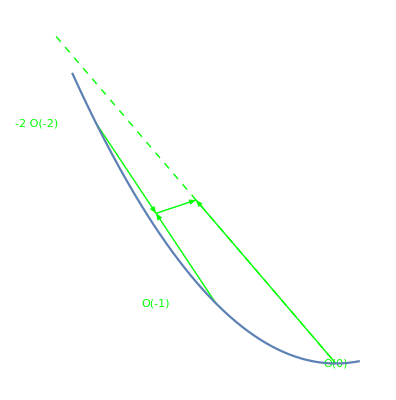

```mathematica
(* Diagram in (s,φ) plane *)
ScattDiagLZ[LiTrees]
```

```mathematica
IndKr=ScattIndex[LiTrees]
```

{Kr_3[1,2] Kr_9[1,1]}

```mathematica
Ind=EvaluateKronecker[IndKr];
Limit[Ind,y->1]
Series[Ind,{y,Infinity,0}]
```

{27}

{y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+O[1/y]^1}

```mathematica
(* When some internal charges are non-primitive, more care is needed to compute the index : *)
LiOm1={y^2+1+1/y^2,-y^5-y^3-y-1/y-1/y^3-1/y^5,y^10+y^8+2y^6+2y^4+2y^2+2+2/y^2+2/y^4+2/y^6+1/y^8+1/y^10};
L21=TropicalVertex[3,{2,1},LiOm1,{1}];
L22=TropicalVertex[3,{2,2},LiOm1,{1}];
L31=TropicalVertex[3,{3,1},LiOm1,{1}];
Series[{L21,L22,L31},{y,Infinity,0}]
```

{y^10+2 y^8+5 y^6+8 y^4+13 y^2+14+O[1/y]^1,-y^13-2 y^11-6 y^9-10 y^7-17 y^5-21 y^3-24 y+O[1/y]^1,y^18+2 y^16+5 y^14+10 y^12+18 y^10+29 y^8+45 y^6+60 y^4+75 y^2+80+O[1/y]^1}

```mathematica
IndModif=IndKr/.{Subscript[Kr, 3][2,2]^2->l22,Subscript[Kr, 3][2,2]->l21/Subscript[Kr, 3][1,2] , Subscript[Kr, 3][3,3]->l31/Subscript[Kr, 3][1,3]};
Ind=EvaluateKronecker[IndModif]/.{l21->L21,l31->L31,l22->L22};
Limit[Ind,y->1]
Series[Ind,{y,Infinity,0}]
```

{27}

{y^10+2 y^8+3 y^6+3 y^4+3 y^2+3+O[1/y]^1}